```mathematica
data=Flatten@Import["C:\\Users\\Sebastian\\Dropbox\\Studie\\Kurser\\Datalogi\\PCSD\\Assignments\\1\\tex\\lots-of-clients_100reqs_zipf0.5.txt","TSV"];
```

```mathematica
fancyData=Nest[
Module[{
nums=TakeWhile[#[[1,2;;]],IntegerQ]
},{
#[[1,(2+Length@nums);;]],
Append[#[[2]],nums]
}]&,{data,{}},25][[2]];
```

```mathematica
latencyData={Length[#],Total[#]/(100*Length[#])}&/@fancyData//N
```

{{1.,13.34},{2.,11.34},{3.,13.36},{4.,33.0075},{5.,17.79},{6.,28.885},{7.,28.96},{8.,23.71},{9.,22.2389},{10.,23.32},{11.,33.0418},{12.,28.755},{13.,60.5831},{14.,69.3593},{15.,71.97},{16.,80.265},{17.,86.7476},{18.,86.5572},{19.,94.8232},{20.,107.317},{21.,36.5852},{22.,39.05},{23.,112.133},{24.,122.311},{25.,128.363}}

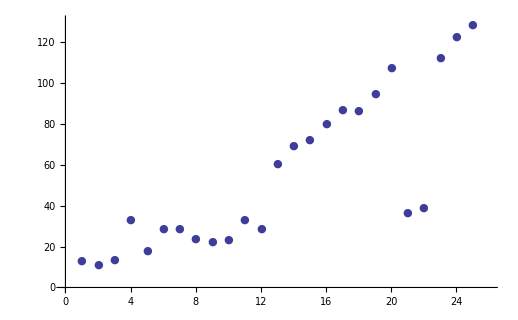

```mathematica
ListPlot[latencyData,PlotRange->{{0,26},{0,130}},PlotMarkers->{Automatic,Small}]
```

```mathematica
throughputData={Length[#],(100*Length[#])/(Total[#]/1000)}&/@fancyData//N
```

{{1.,74.9625},{2.,88.1834},{3.,74.8503},{4.,30.2961},{5.,56.2114},{6.,34.62},{7.,34.5304},{8.,42.1763},{9.,44.9663},{10.,42.8816},{11.,30.2647},{12.,34.7766},{13.,16.5063},{14.,14.4177},{15.,13.8947},{16.,12.4587},{17.,11.5277},{18.,11.5531},{19.,10.5459},{20.,9.31823},{21.,27.3334},{22.,25.6082},{23.,8.91798},{24.,8.17589},{25.,7.79042}}

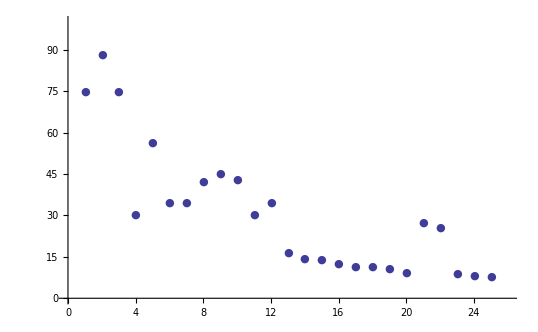

```mathematica
ListPlot[throughputData,PlotRange->{{0,26},{0,100}},PlotMarkers->{Automatic,Small}]
```